# CHAPTER 1 DISCRETE PROBABILITY

## 1.1 The Cast of Characters

Why study probability? All around us is uncertainty and we must understand its nature in order to conduct ourselves in the world. We join the shortest waiting line in hopes that it has the best chance of allowing us to be served quickly.  We invest our savings in assets that we believe are most likely to yield high returns.  We buy the battery that we think is most likely to last the longest.  The study of probability also lets you understand the mechanics of games of chance like roulette, poker, and blackjack; what is predictable and what is not, what to bet on (usually nothing) and what not to bet on (usually everything).  In all of these cases we do not know for certain what will happen before the phenomenon is observed (we don't know how much time we will wait in line, what our opponent's blackjack hand will be, etc.).  But some common-sense assumptions, background knowledge, or a long history of observed data from similar experiments can enable us to quantify likelihoods.  Several of these examples have actually given birth to significant subfields of probability or related areas of study, for example, queueing theory (i.e., the study of waiting lines) and mathematical finance, which are introduced in Chapter 6.   Probability also provides the theoretical basis for statistics, which is the art of using data obtained randomly to draw conclusions about social and scientific phenomena. 
	In addition to all this, probability exhibits many of the aesthetically appealing properties that attract people to mathematics in general. It proceeds logically from a few simple axioms to build an abstract structure which is straightforward, yet powerful. The cast of characters of probability is both foreign and tangible, which implies that you must work a little to get to know them, but there is hope in succeeding in the acquaintance.
	This text will be somewhat different from others in the field. While the main ideas of probability have not changed much in at least fifty years, the world has, and learning in mathematics has changed with it.  Many things are technologically possible today of which mathematics education should take advantage.  This book is a living, interactive text which asks you to do activities as you read carefully to help you understand and discover the ideas of probability in new ways, on your own terms.  The complete text is available electronically in the form of Mathematica notebooks, one for each section.  The notebooks are executable, so that you can reenter existing commands, modify them, or write your own supplemental commands to take the study in the direction you wish. You will be building probability yourself in a kind of workshop, with Mathematica and your own insight and love of experimentation as your most powerful tools.  I caution you against depending too much on the machine, however.  Much of the time, traditional pencil, paper, and brainpower are what you need most to learn.  What the computer does, however, is open up new problems, or let you get new insights into concepts.  So we will be judiciously blending new technology with traditionally successful pedagogy to enable you to learn effectively.  Consistent themes will be the idea of taking a sample randomly from a larger universe of objects in order to get information about that universe, and the computer simulation of random phenomena to observe patterns in many replications that speak to the properties of the phenomena. 
	The cast of characters in probability whose personalities we will explore in depth in the coming chapters include the following six principal players: (1) Event; (2) Sample Space; (3) Probability Measure; (4) Random Variable; (5) Distribution; and (6) Expectation.  The rest of this section will be a brief intuitive introduction to these six. 
	Most of the time we are interested in assessing likelihoods of events, that is, things that we might observe as we watch a phenomenon happen. The event that a national chain's bid to acquire a local grocery store is successful, the event that at least 10 patients arrive to an emergency room between 6:00 and 7:00 AM, the event that a hand of five poker cards forms a straight, the event that we hold the winning ticket in the lottery, and the event that two particular candidates among several are selected for jury duty are just a few examples. They share the characteristic that there is some uncertain experiment, sampling process, or phenomenon whose result we do not know "now". But there is a theoretical "later" at which we can observe the phenomenon taking place, and decide whether the event did or didn't occur.
	An outcome (sometimes called a simple event) is an event that cannot be broken down into some combination of other events. A composite event is just an event that isn't simple, that is, it has more than one outcome. For instance the event that we are dealt a poker hand that makes up a straight is composite because it consists of many outcomes which completely specify the hand, such as 2 through 6 of hearts, 10 through ace of clubs, etc. 
	This is where the sample space makes its entry: the sample space is the collection of all possible outcomes of the experiment or phenomenon, that is all possible indecomposable results that could happen.  For the poker hand example, the sample space would consist of all possible five-card hands. In specifying sample spaces, we must be clear about assumptions; for instance we might assume that the order in which the cards were dealt does not matter, and we cannot receive the same card twice, so that the cards are dealt without replacement.

Activity 1  How can you characterize the sample space for the grocery store example?  Make up your own random phenomenon, informally describe the sample space, and give examples of events.

Activity 2  In the emergency room example above, is the event that was described an outcome or a composite event?  If that event is composite, write down an example of an outcome relating to that phenomenon.

In random phenomena, we need a way of measuring how likely the events are to occur. This may be done by some theoretical considerations, or by experience with past experiments of the same kind. A probability measure assigns a likelihood, that is a number between 0 and 1, to all events. Though we will have to be more subtle later, for now we can intuitively consider the extremes of 0 and 1 as representing impossibility and complete certainty, respectively. 
	Much of the time in probability problems, probability measures are constructed so that the probability of an event is the "size" of the event as a proportion of the "size" of the whole sample space. "Size" may mean different things depending on the context, but the two most frequent usages are cardinality, that is number of elements of a set, and length (or area in two dimensions). For example, if you roll a fair die once, since there are six possible faces that could land on top, the sample space is {1,2,3,4,5,6}. Since three of the faces are odd, it seems reasonable that the probability that an odd number is rolled is 3/6. Size means length in the following scenario. Suppose that a real number is to be randomly selected in the interval [0,4]. This interval is the sample space for the random phenomenon. Then the probability that the random real number will be in the interval [1,3] is 2/4=1/2, which is the length of the interval [1,3] divided by the length of the whole sample space interval. 
	The first two chapters will concentrate on discrete probability, in which counting the number of elements in sets is very important. We will leave much of the detail for later sections, except to remind you of the intuitively obvious multiplication principle for counting. If outcomes of a random experiment consist of two stages, then the total number of outcomes of the experiment is the number of ways the first stage can occur times the number of ways that the second can occur. This generalizes to multiple stage experiments. For instance, if a man has 3 suits, 6 shirts, and 4 ties, and he doesn't care about color coordination and the like, then he has 3×6×4=72 possible outfits. 
	It is possible to experimentally estimate a probability by repeating the experiment over and over again. The probability of the event can be estimated by the number of times that it occurs among the replications divided by the number of replications.  Try this exercise. In the KnoxProb7`Utilities` package that you should have installed is a Mathematica command called 

			DrawIntegerSample[a, b, n] 
 
which outputs a sequence of n numbers drawn at random, without reusing numbers previously in the sequence, from the positive integers in the range a, ... , b.  (You should be sure that the package has been loaded into the ExtraPackages subdirectory within the Mathematica directory you are using on your computer.)  First execute the command to load the package, then try repeating the experiment of drawing samples of two numbers from {1,... ,5} a large number of times. I have shown one such sample below. Keep track of how frequently the number 1 appears in your samples. Empirically, what is a good estimate of the probability that 1 is in the random sample of size two? Talk with a group of your classmates, and see if you can set up a good theoretical foundation that supports your conclusion. (Try to specify the sample space of the experiment.)  We will study this type of experiment more carefully later in this chapter.  Incidentally, recall that Mathematica uses braces { } to delineate sequences as well as unordered sets. We hope that the context will make it clear which is meant; here the integer random sample is assumed to be in sequence, so that, for example, {1,3} is different from {3,1}.

```mathematica
Needs["KnoxProb7`Utilities`"]
```

```mathematica
DrawIntegerSample[1,5,2]
```

{3,2}

We are halfway through our introduction of the cast of characters. Often the outcomes of a random phenomenon are not just numbers. They may be sequences of numbers as in our sampling experiment, or even non-numerical data such as the color of an M&M that we randomly select from a bag. Yet we may be interested in encoding the simple events by single numbers, or extracting some single numerical characteristic from more complete information. For example, if we are dealt a five card hand in poker, an outcome is a full specification of all five cards, whereas we could be interested only in the number of aces in the hand, which is a numerical valued function of the outcome. Or, the sample space could consist of subjects in a medical experiment, and we may be interested in the blood sugar level of a randomly selected subject. Such a function for transforming outcomes to numerical values is called a random variable, the fourth member of our cast of characters. Since the random variable depends on the outcome, and we do not know in advance what will happen, the value of the random variable is itself uncertain until after the experiment has been observed.

Activity 3  Use DrawIntegerSample again as below to draw samples of size five from a population of size 50.  Suppose we are interested in the random variable which gives the minimum among the members of the sample. What values of this random variable do you observe in several replications?

```mathematica
outcome=DrawIntegerSample[1,50,5]
X=Min[outcome]
```

The cell below contains a command I have called SimulateMinima for observing a number m of values of the minimum random variable from Activity 3.  Read the code carefully to understand how it works. An integer sample is drawn from the set {1,2,...,popsize}, and then its minimum is taken. The Table command assembles a list of m of these minima. To get an idea of the pattern of those sample minima, we plot a graph called a histogram which tells the proportion of times among the m replications of the experiment that the sample minimum fell into each of a given number of categories. The Histogram command is in the kernel in Mathematica 7.  Its exact syntax is

			Histogram[listofdata, binspecifications, barheightspecifications]		
		
where the latter two arguments are optional. (See the help documentation, the note in the preface, and the appendix on Mathematica commands for version 6 of Mathematica and the KnoxProb6`Utilities` package.)  The binspecifications argument can be set to be a number for a desired number of categories, or it can be set to a list {d w} for a desired category width. The third argument can be set to "Count," "Probability," or "ProbabilityDensity," respectively, to force the bar heights to be freqencies, relative frequencies, or relative frequencies divided by category widths. One output cell is shown in Figure 1 using 100 replications, six histogram rectangles, and using samples of size 5 from {1, ... , 50}. You should reexecute several times to see whether your replications give similar histograms. Should they be identical to this one? Why or why not? (If you want to suppress the list of minima and get only the histogram, put a semicolon between the SimulateMinima and Histogram commands.)

```mathematica
SimulateMinima[m_,popsize_,sampsize_]:=
	Table[Min[DrawIntegerSample[1,popsize,sampsize]],{i,1,m}]
```

```mathematica
mins=SimulateMinima[100,50,5]
Histogram[mins,6]
```

{8,1,2,1,11,4,23,5,1,17,1,3,1,4,11,2,12,13,10,9,7,4,11,1,6,5,12,2,9,3,28,12,16,7,4,3,3,6,19,1,15,4,21,1,6,26,15,11,9,2,2,8,4,1,1,4,9,9,12,5,11,7,11,31,3,7,13,19,4,8,21,11,17,10,6,5,5,16,12,5,16,9,22,2,8,13,3,3,15,6,2,6,8,22,19,1,4,13,8,4}

-Graphics-

Figure 1.1 - Sample histogram of minimum of five values from {1,2,... ,50}

The histogram for the sample minimum that we just saw, together with your experiments, hints at a very deep idea, which is the fifth member of our cast. A random variable observed many times will give a list of values that follows a characteristic pattern, with some random variation. The relative frequencies of occurrence (that is the number of occurrences divided by the number of replications) of each possible value of the random variable, which are the histogram rectangle heights, will stabilize around some theoretical probability. Much as a probability measure can be put on a sample space of simple events, a probability distribution can be put on the collection of possible values of a random variable. To cite a very simple example, if 1/3 of the applicants for a job are men and 2/3 are women, if one applicant is selected randomly, and if we define a random variable

X = {1   if applicant is a man
0   if applicant is a woman

then the two possible values of X are 1 and 0, and the probability distribution for this X gives probability 1/3 to value 1 and 2/3 to value 0. 
	The last member of our cast is expectation or expected value of a random variable.  Its purpose is to give a single number which is an average value that the random variable can take on.  But if these possible values of the random variable are not equally likely, it doesn't make sense to compute the average as a simple arithmetical average.  For example, suppose the number of 911 emergency calls during an hour is a random variable X whose values and probability distribution are as in the table below.

value of X | 2 | 4 | 6 | 8
probability | 1/10 | 2/10 | 3/10 | 4/10

What could we mean by the average number of calls per hour?  The simple arithmetical average of the possible values of X is (2+4+6+8)/4 = 5, but 6 and 8 are more likely than 2 and 4, so they deserve more influence. In fact, the logical thing to do is to define the expected value of X, denoted by E[X], to be the weighted average of the possible values, using the probabilities as weights:

E[X]=1/10×2+2/10×4+3/10×6+4/10×8 = 60/10 = 6

We will be looking at all of our characters again in a more careful way later, but I hope that the seeds of intuitive understanding have been planted. You should reread this introductory section from time to time as you progress to see how the intuition fits with the formality.

### Exercises 1.1

1. Most state lotteries have a version of a game called Pick 3 in which you win an amount, say $500, if you correctly choose three digits in order.  Suppose that the price of a Pick 3 ticket is $1.  There are two possible sample spaces that might be used to model the random experiment of observing the outcome of the Pick 3 experiment, according to whether the information of the winning number is recorded, or just the amount you won.  Describe these two sample spaces clearly, give examples of outcomes for both, and describe a reasonable probability measure for both.

2. A grand jury is being selected, and there are two positions left to fill, with candidates A, B, C, and D remaining who are eligible to fill them.  The prosecutor decides to select a pair of people by making slips of paper with each possible pair written on a slip, and then drawing one slip randomly from a hat. List out all outcomes in the sample space of this random phenomenon, describe a probability measure consistent with the stated assumptions, and find the probability that A will serve on the grand jury.

3. In an effort to predict performance of entering college students in a beginning mathematics course on the basis of their mathematics ACT score, the following data were obtained. The entries in the table give the numbers of students among a group of 179 who had the indicated ACT score and the indicated grade.

Grade
ACT     | A | B | C | D | F
23 | 2 | 5 | 16 | 31 | 3
24 | 6 | 8 | 12 | 15 | 2
25 | 7 | 10 | 15 | 6 | 1
26 | 8 | 15 | 13 | 4 | 0

(a) A student is selected randomly from the whole group. What is the probability that this student has a 25 ACT and received a B?  What is the probability that this student received a C?  What is the probability that this student has an ACT score of 23?

(b) A student is selected randomly from the group of students who scored 24 on the ACT.  What is the probability that this student received an A?

(c) A student is selected randomly from the group of students who received B's.  What is the probability that the student scored 23 on the ACT?  Is it the same as your answer to the last question in part (a)?

4. Find the sample space for the following random experiment. Four people labeled A, B, C, and D are to be separated randomly into a group of 2 people and two groups of one person each.  Assume that the order in which the groups are listed does not matter, only the contents of the groups.

5. Consider the experiment of dealing two cards from a standard 52 card deck (as in blackjack), one after another without replacing the first card.  Describe the form of all outcomes, and give two examples of outcomes. What is the probability of the event "King on 1st card?"  What is the probability of the event "Queen on 2nd card?"

6.  In the Pick 3 lottery example of Exercise 1, consider the random variable X that gives the net amount you win if you buy one ticket (subtracting the ticket price).  What is the probability distribution of X? What is the expected value of X?

7.  An abstract sample space has outcomes a, b, c, d, e, and f as shown on the left in the figure. Each outcome has probability 1/6. A random variable X maps the sample space to the set {0,1} as in the diagram. What is the probability distribution of X?  What is the expected value of X?

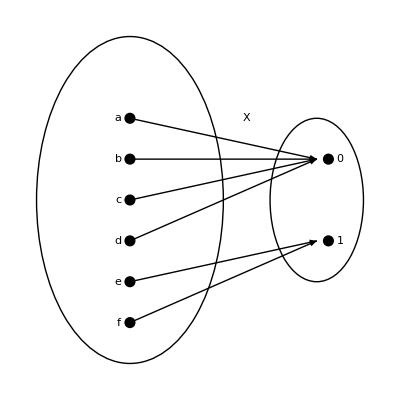

```mathematica
g1=Graphics[{Circle[{11,4},2],Circle[{3,4},4]}];
g2=Graphics[{PointSize[0.02],Point[{11.5,3}],Point[{11.5,5}],Point[{3,1}],Point[{3,2}],Point[{3,3}],Point[{3,4}],Point[{3,5}],Point[{3,6}]}];
g3=Graphics[{Arrow[{{3,6},{11,5}}],Arrow[{{3,5},{11,5}}],Arrow[{{3,4},{11,5}}],Arrow[{{3,3},{11,5}}],Arrow[{{3,2},{11,3}}],Arrow[{{3,1},{11,3}}]}];
g4=Graphics[{Text[a,{2.5,6}],Text[b,{2.5,5}],Text[c,{2.5,4}],Text[d,{2.5,3}],Text[e,{2.5,2}],Text[f,{2.5,1}],Text[0,{12,5}],Text[1,{12,3}],Text[Style[X,Medium],{8,6}]}];
Show[{g1,g2,g3,g4},AspectRatio->1,BaseStyle->{10,FontFamily->"Times"}]
```

Exercise 7

8. Two fair coins are flipped at random and in succession.  Write the sample space explicitly, and describe a reasonable probability measure on it.  If X is the random variable that counts the number of heads, find the probability distribution of X and compute the expected value of X.

9.  Using the data in Exercise 3, give an empirical estimate of the probability distribution of the random variable X that gives the ACT score of a randomly selected student.  What is the expected value of X, and what is its real meaning in this context?

10. (Mathematica)  Use the DrawIntegerSample command introduced in the section to build a command that draws a desired number of samples, each of a desired size, from the set {1,2,...,popsize}.  For each sample, the command appends the maximum number in the sample to a list.  This list can be used to create a histogram of the distribution of maxima.  Repeat the experiment of taking 50 random samples of size 4 from {1,2,... ,7} several times. Describe in words the most salient features of the histograms of the maximum.  Use one of your replications to give an empirical estimate of the probability distribution of the maximum.

11. (Mathematica)  The command SimulateMysteryX[m] illustrated below will simulate a desired number m of values of a mystery random variable X.  First load the KnoxProb7`Utilities` package, then run the command several times using specific numerical values for m.  Try to estimate the probability distribution of X and its expected value.

```mathematica
SimulateMysteryX[10]
```

12. (Mathematica)  Write a command in Mathematica which can take as input a list of pairs {p_i, x_i} in which a random variable X takes on the value x_i with probability p_i and return the expectation of X.  Test your command on the random variable whose probability distribution is in the table below.

value of X | 0 | 1 | 2 | 3
probability | 1/4 | 1/2 | 1/8 | 1/8

13. Two flights are selected randomly and in sequence from a list of departing flights covering a single day at an airport.  There were 100 flights in the list, among which 80 departed on time, and 20 did not. Write a description of the sample space of the experiment of selecting the two flights, and use the multiplication principle to count how many elements the sample space has.  Now let X be the number of flights in the sample of two that were late.  Find the probability distribution of X.